```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
```

plot2Doption

importData

jsonInfo

```mathematica
surgeExp=Import[FileNameJoin[{NotebookDirectory[],"surge.csv"}]];
tensionExp=Import[FileNameJoin[{NotebookDirectory[],"tension1.csv"}]];
heaveExp=Import[FileNameJoin[{NotebookDirectory[],"heave.csv"}]];
pitchExp=Import[FileNameJoin[{NotebookDirectory[],"pitch.csv"}]];
```

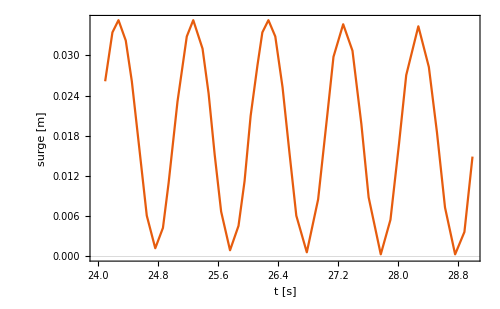

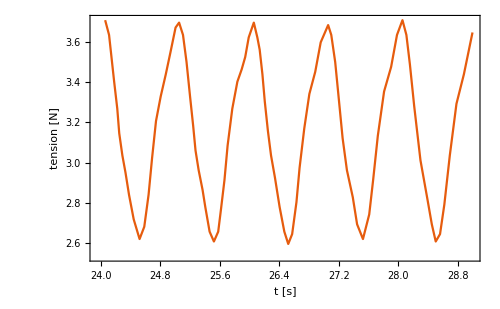

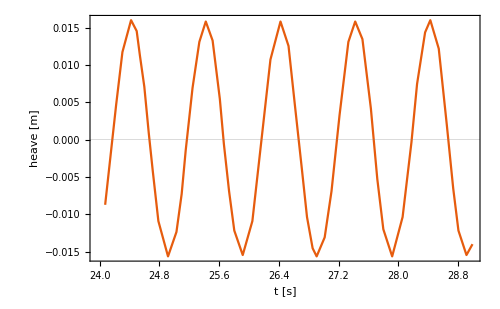

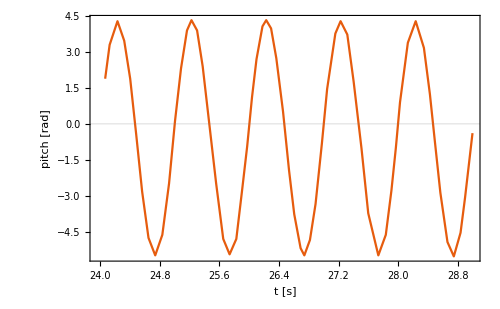

```mathematica
ListPlot[surgeExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}]
ListPlot[tensionExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","tension [N]"}]
ListPlot[heaveExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}]
ListPlot[pitchExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}]
```

~/BEM/Palm2016_with_mooring/result.json

no. | title | length
1 | cpu_time | 432
2 | float_COM | 432
3 | float_EK | 432
4 | float_EP | 432
5 | float_accel | 432
6 | float_area | 432
7 | float_force | 432
8 | float_pitch | 432
9 | float_roll | 432
10 | float_torque | 432
11 | float_velocity | 432
12 | float_yaw | 432
13 | simulation_time | 432
14 | wall_clock_time | 432
15 | water_E | 432
16 | water_EK | 432
17 | water_EP | 432
18 | water_face_size | 432
19 | water_point_size | 432
20 | water_volume | 432

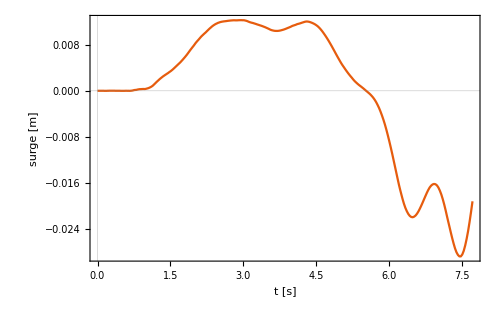

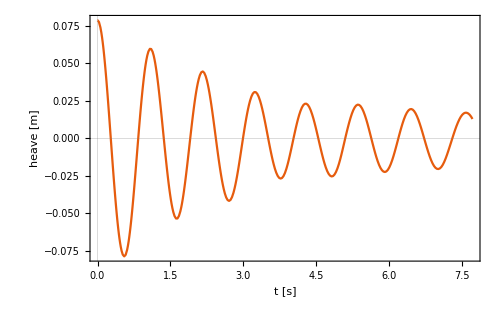

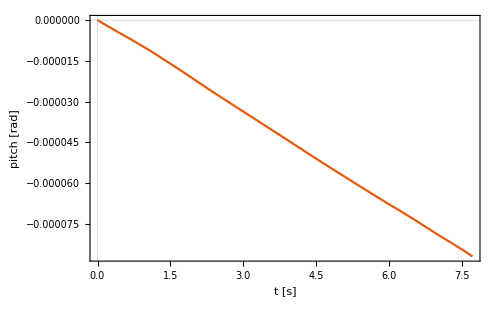

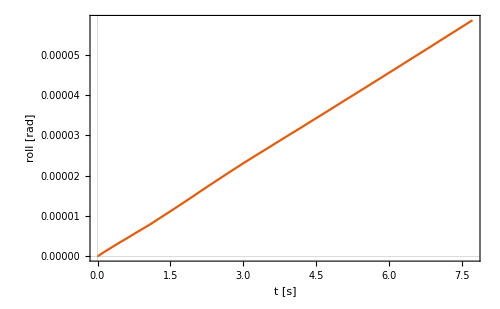

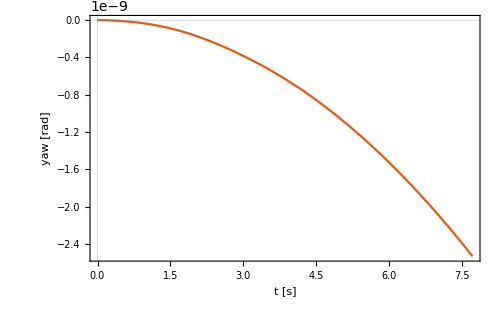

```mathematica
(*nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"*)
nameSim="~/BEM/Palm2016_with_mooring/result.json"
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

ListPlot[Transpose@{time,surgeSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}]
ListPlot[Transpose@{time,heaveSim-0.725},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}]
ListPlot[Transpose@{time,pitchSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}]
ListPlot[Transpose@{time,rollSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","roll [rad]"}]
ListPlot[Transpose@{time,yawSim},Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","yaw [rad]"}]
```